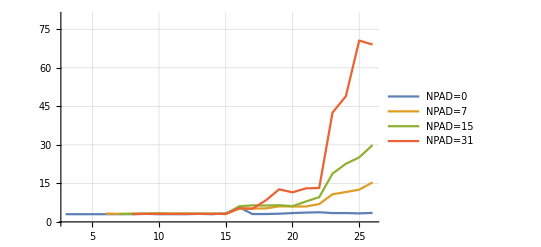

```mathematica
NPAD0Linear={{3,3},{4,3},{5,3},{6,3},{7,3},{8,3},{9,3.125},{10,3},{11,3},{12,3},{13,3.125},{14,3},{15,3.3125},{16,5.6875},{17,3.0625},{18,3.0625},{19,3.1875},{20,3.4375},{21,3.625},{22,3.75},{23,3.4375},{24,3.4375},{25,3.3125},{26,3.5},};
NPAD7Linear={{6,3.25},{7,3.125},{8,3.125},{9,3.125},{10,3.25},{11,3.125},{12,3.125},{13,3.125},{14,3.1875},{15,3.0625},{16,5.125},{17,5.1875},{18,5.25},{19,6.0625},{20,6},{21,6},{22,6.9375},{23,10.75},{24,11.625},{25,12.5625},{26,15.375},};
NPAD15Linear={{7,3.0625},{8,3.1875},{9,3.1875},{10,3.3125},{11,3.1875},{12,3.25},{13,3.1875},{14,3.1875},{15,3.0625},{16,6.0625},{17,6.4375},{18,6.375},{19,6.5},{20,6.125},{21,7.9375},{22,9.625},{23,18.8125},{24,22.625},{25,25.125},{26,29.9375},};
NPAD31Linear={{8,3.0625},{9,3.125},{10,3.125},{11,3.125},{12,3.125},{13,3.125},{14,3.125},{15,3.125},{16,5.3125},{17,5.125},{18,8.375},{19,12.6875},{20,11.5},{21,13.0625},{22,13.1875},{23,42.5625},{24,48.9375},{25,70.625},{26,69.0625},};
ListPlot[{NPAD0Linear,NPAD7Linear,NPAD15Linear,NPAD31Linear},GridLines->Automatic,Ticks->Automatic,Joined->True,PlotLegends->{"NPAD=0", "NPAD=7","NPAD=15","NPAD=31"},PlotRange->80]
```

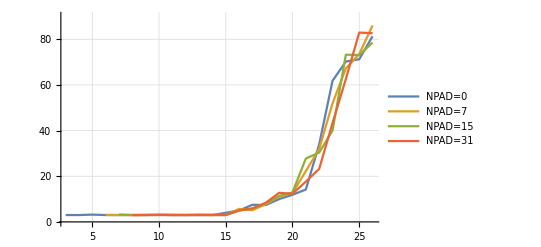

```mathematica
NPAD0Random={{3,3},{4,3},{5,3.1875},{6,3},{7,3},{8,3},{9,3.0625},{10,3},{11,3},{12,3},{13,3},{14,3},{15,4},{16,5},{17,7.5},{18,7.375},{19,10},{20,11.875},{21,14.1875},{22,33.9375},{23,61.8125},{24,70.25},{25,71.25},{26,81.3125},};
NPAD7Random={{6,3.0625},{7,3},{8,3},{9,3},{10,3.0625},{11,3},{12,3.0625},{13,3.125},{14,3.125},{15,3.0625},{16,5.6875},{17,5.125},{18,7.75},{19,11.125},{20,12.5625},{21,22.25},{22,31.9375},{23,51.9375},{24,67.25},{25,73.5},{26,86.0625},};
NPAD15Random={{7,3.25},{8,3},{9,3},{10,3.0625},{11,3.125},{12,3},{13,3.125},{14,3},{15,3},{16,5},{17,5.75},{18,8.25},{19,11.375},{20,12.9375},{21,27.75},{22,30.375},{23,40},{24,73.25},{25,73.125},{26,78.5625},};
NPAD31Random={{8,3},{9,3},{10,3.125},{11,3},{12,3},{13,3},{14,3},{15,3},{16,5},{17,5.9375},{18,8.375},{19,12.75},{20,12.3125},{21,17.625},{22,23.25},{23,43.3125},{24,62.625},{25,82.9375},{26,82.6875},};
ListPlot[{NPAD0Random,NPAD7Random,NPAD15Random,NPAD31Random},GridLines->Automatic,Ticks->Automatic,Joined->True,PlotLegends->{"NPAD=0", "NPAD=7","NPAD=15","NPAD=31"},PlotRange->90]
```

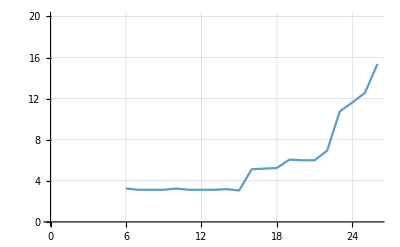

```mathematica
ListLinePlot[NPAD7Linear,GridLines->Automatic,PlotRange->20]
```